## G(T) for p0=3.75

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p3.750/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.02,0.016 ,0.014,0.012,0.011,0.01,0.0093, 0.008 ,0.0063,0.005,0.00385};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.02000000,0.01600000,0.01400000,0.01200000,0.01100000,0.01000000,0.00930000,0.00800000,0.00630000,0.00500000,0.00385000}

```mathematica
spacing={22,22,23,25,40,34,400,400,400,247,400,287,393,400,400,400};
```

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.7500_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.741965,0.58808,0.523112,0.465745,0.409941,0.355336,0.320942,0.275636,0.251092,0.228001,0.213735,0.19105,0.164743,0.143155,0.122044}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.541302,0.476831,0.435691,0.40896,0.378599,0.328808,0.304247,0.265896,0.241394,0.19775,0.214215,0.136959,0.0859052,0.0842281,0.0706463}

```mathematica
g1Mean=Table[Mean[Table[Mean[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{-0.000805251,-0.0000992515,0.000034431,-0.000546891,0.000114737,0.000610911,-0.00107302,0.00257268,0.00215251,0.00258835,0.00399716,0.0811209,0.0422781,0.00625063,0.037048}

```mathematica
g1s=Table[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}],{T,Length[Tlist]}]
```

{{0.741786,0.74199,0.742119},{0.587871,0.588096,0.588273},{0.523209,0.522985,0.52314},{0.465987,0.4656,0.465649},{0.409948,0.410006,0.409868},{0.355259,0.355417,0.355331},{0.320986,0.321122,0.320719},{0.275914,0.275386,0.275609},{0.251532,0.250655,0.25109},{0.228447,0.227403,0.228152},{0.212495,0.215326,0.213384},{0.189953,0.192607,0.190591},{0.164908,0.164182,0.165139},{0.144253,0.142571,0.142641},{0.122337,0.122197,0.121597}}

```mathematica
g2s=Table[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{{0.536542,0.538772,0.548593},{0.481173,0.480463,0.468857},{0.434063,0.441595,0.431415},{0.406764,0.408317,0.411799},{0.386928,0.363858,0.38501},{0.330174,0.333176,0.323074},{0.303955,0.307279,0.301509},{0.267838,0.264277,0.265573},{0.236388,0.237213,0.250582},{0.196023,0.20518,0.192046},{0.217305,0.271678,0.153664},{0.0887847,0.229144,0.0929484},{0.0912248,0.0825648,0.0839262},{0.093987,0.0737283,0.084969},{0.066641,0.0797684,0.0655296}}

```mathematica
Length[derivatives[[11,1,2]]]/2
```

25000

```mathematica
Variance[Normal[derivatives[[11,3,1]]*4096][[Floor[Length[derivatives[[11,3,2]]]/2];;]]]/4096/Tlist[[11]]
```

0.153664

```mathematica
Mean[Normal[derivatives[[10,3,2]]][[Floor[Length[derivatives[[10,3,2]]]/2];;]]]/4096
```

0.228152

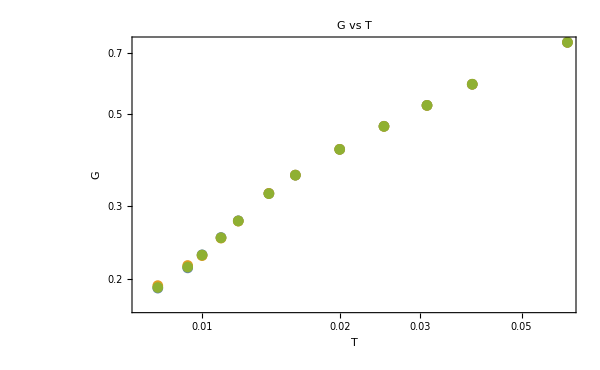

```mathematica
G1Plot=ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

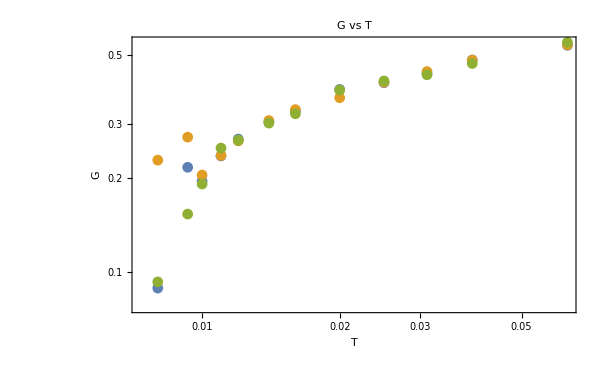

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g2s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

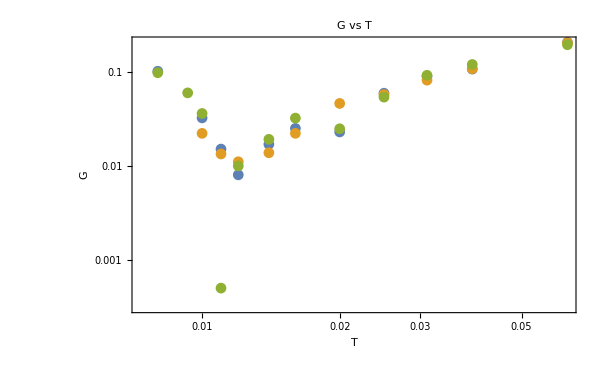

```mathematica
ListLogLogPlot[Table[Table[{Tlist[[T]],g1s[[T,i]]-g2s[[T,i]]},{T,12}],{i,3}],FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T"]
```

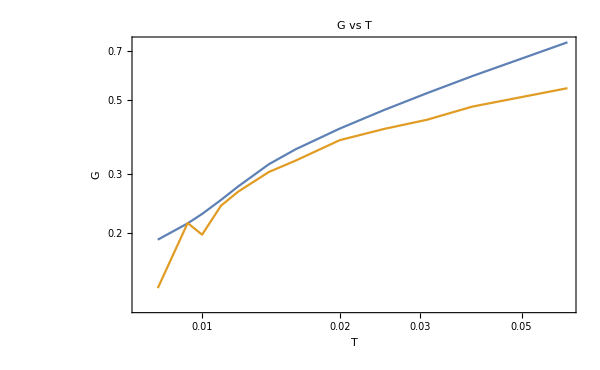

```mathematica
GPlot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,12}],Table[{Tlist[[T]],g2[[T]]},{T,12}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

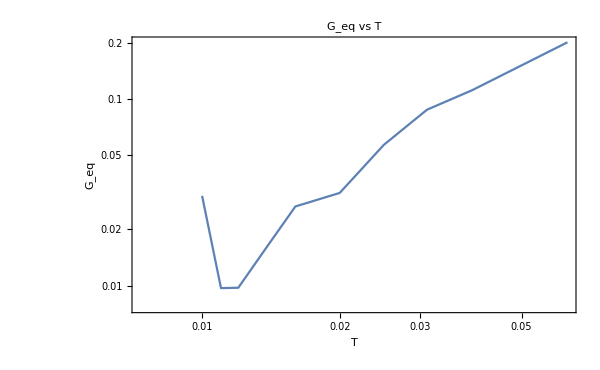

```mathematica
GeqPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,12}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### fitting

```mathematica
GT[A_,T_,B_]:=A T^B;
```

```mathematica
g1fitting1=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,5}],{GT[A,t,B]},{A,B},t]
```

FittedModel[3.04179 t^0.508891]

```mathematica
g1fitting2=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]},{T,6,12}],{GT[A,t,B]},{A,B},t]
```

FittedModel[16.8174 t^0.930924]

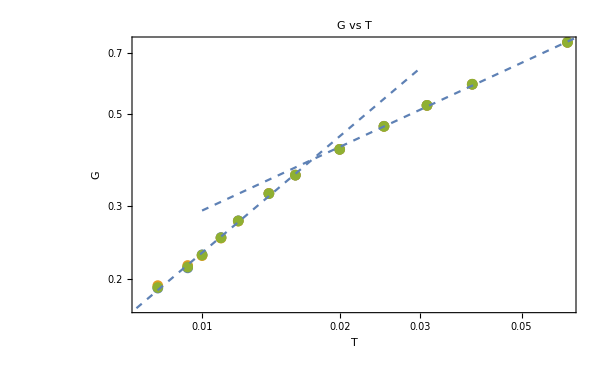

```mathematica
Show[G1Plot,LogLogPlot[g1fitting1[x],{x,0.01,0.1},PlotStyle->Dashed],LogLogPlot[g1fitting2[x],{x,0.0001,0.03},PlotStyle->Dashed]]
```

```mathematica
geqfitting=NonlinearModelFit[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,9}],{GT[A,t,B]},{A,B},t]
```

FittedModel[10.9883 t^1.43862]

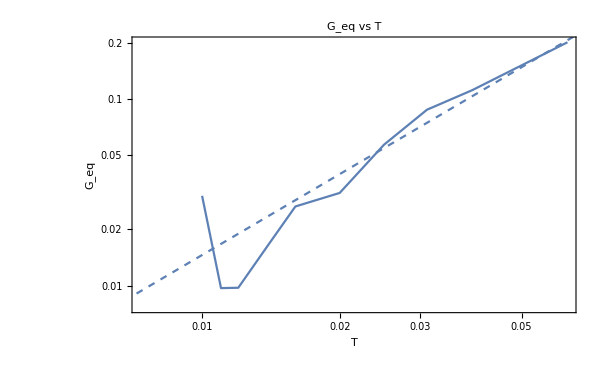

```mathematica
Show[GeqPlot,LogLogPlot[geqfitting[x],{x,0.0005,0.1},PlotStyle->Dashed,PlotLegends->Automatic]]
```